```mathematica
Clear[A1,A2,B1,B2]
G1[A1_,A2_,B1_,B2_]=1/(1/A1 + 1/B1*(A2/A1));
G2[A1_,A2_,B1_,B2_]=1/(1/B2 + 1/A2*(B1/B2));
M=4;
μ[A1_,A2_,B1_,B2_]=(A1*B1-A2*B2)/(A1+A2+B1+B2);
Diffusion[A1_,A2_,B1_,B2_]=((A1*B1+A2*B2)-2μ[A1,A2,B1,B2]^2)/(2*(A1+A2+B1+B2));
```

```mathematica
Clear[a,b,s1,s2];

A1= a Exp[ s1/2];
A2= a Exp[-  s1/2];
B1=b Exp[ s2/2];
B2= b Exp[- s2/2];
FullSimplify[μ[A1,A2,B1,B2]]
Diffusion[A1,A2,B1,B2]
FullSimplify[Diffusion[A1,A2,B1,B2]/μ[A1,A2,B1,B2]]

G1[a1,a2,a1,a2]-G2[a1,a2,a1,a2]
```

(a b Sinh[(s1+s2)/2])/(a Cosh[s1/2]+b Cosh[s2/2])

(a b ⅇ^(-s1/2-s2/2)+a b ⅇ^(s1/2+s2/2)-(2 (-a b ⅇ^(-s1/2-s2/2)+a b ⅇ^(s1/2+s2/2))^2)/((a ⅇ^(-s1/2)+a ⅇ^(s1/2)+b ⅇ^(-s2/2)+b ⅇ^(s2/2))^2))/(2 (a ⅇ^(-s1/2)+a ⅇ^(s1/2)+b ⅇ^(-s2/2)+b ⅇ^(s2/2)))

(a^2 ⅇ^s2 (1+ⅇ^s1)^2 (1+ⅇ^(s1+s2))+b^2 ⅇ^s1 (1+ⅇ^s2)^2 (1+ⅇ^(s1+s2))+4 a b ⅇ^((3 (s1+s2))/2) (2+Cosh[s1]+Cosh[s2]))/(2 (-1+ⅇ^(s1+s2)) (a ⅇ^(s2/2) (1+ⅇ^s1)+b ⅇ^(s1/2) (1+ⅇ^s2))^2)

-1/(a1/a2^2+1/a2)+1/(1/a1+a2/a1^2)

```mathematica
Simplify[-1/(a1/a2^2+1/a2)+1/(1/a1+a2/a1^2)]
```

a1-a2

```mathematica
a=1;b=1;
Plot3D[1/((a^2 ⅇ^s2 (1+ⅇ^s1)^2 (1+ⅇ^(s1+s2))+b^2 ⅇ^s1 (1+ⅇ^s2)^2 (1+ⅇ^(s1+s2))+4 a b ⅇ^((3 (s1+s2))/2) (2+Cosh[s1]+Cosh[s2]))/(2 (-1+ⅇ^(s1+s2)) (a ⅇ^(s2/2) (1+ⅇ^s1)+b ⅇ^(s1/2) (1+ⅇ^s2))^2)),{s1,0,30},{s2,0,30},PlotRange->Full,AxesLabel->{"s_a","s_b","μ/D"}]
```

-Graphics3D-

```mathematica
a=1;b=100;
Plot3D[1/((a^2 ⅇ^s2 (1+ⅇ^s1)^2 (1+ⅇ^(s1+s2))+b^2 ⅇ^s1 (1+ⅇ^s2)^2 (1+ⅇ^(s1+s2))+4 a b ⅇ^((3 (s1+s2))/2) (2+Cosh[s1]+Cosh[s2]))/(2 (-1+ⅇ^(s1+s2)) (a ⅇ^(s2/2) (1+ⅇ^s1)+b ⅇ^(s1/2) (1+ⅇ^s2))^2)),{s1,-30,30},{s2,-30,30},PlotRange->Full,AxesLabel->{"s_a","s_b","μ/D"}]
```

-Graphics3D-

```mathematica
Series[ArcTanh[x],{x,0,10}]
```

x+x^3/3+x^5/5+x^7/7+x^9/9+O[x]^11

```mathematica
Coth[x]*Tanh[x]
```

1

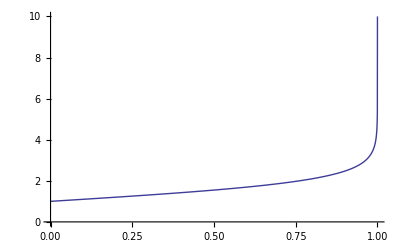

```mathematica
Plot[1+ArcTanh[x],{x,0,1},PlotRange->{0,10}]
```

```mathematica
a=1;b=10;Plot3D[1-((4 a b Cosh[(s1+s2)/4])/(a Cosh[s1/2]+b Cosh[s2/2]))^2,{s1,-30,30},{s2,-30,30},PlotRange->Full]
```

-Graphics3D-

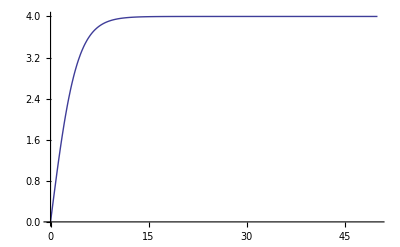

```mathematica
a=1;b=1;s1=0;
s1=s/2;
s2=s/2;
Plot[μ[A1,A2,B1,B2]/Diffusion[A1,A2,B1,B2],{s,0,50},PlotRange->Full]
```

```mathematica
1/4 Coth[s/4]
a
```

1/4 Coth[s/4]

a

```mathematica
FullSimplify[ ((A1 B1+A2 B2)/(2 (A1 B1 -A2 B2))-(A1 B1-A2 B2)/(A1+A2+B1+B2)^2)/(Coth[(s1+s2)/4]/4)]
```

(2 (a^2 ⅇ^s (1+ⅇ^s) (1+ⅇ^s1)^2+b^2 (1+ⅇ^s) (ⅇ^s+ⅇ^s1)^2+4 a b ⅇ^((3 s)/2+s1) (2+Cosh[s-s1]+Cosh[s1])) Tanh[s/4])/((-1+ⅇ^s) (a ⅇ^(s/2) (1+ⅇ^s1)+b (ⅇ^s+ⅇ^s1))^2)

```mathematica
FullSimplify[(A1 B1+A2 B2)/(2 (A1 B1 -A2 B2))/(Coth[(s1+s2)/4]/4)]
```

Cosh[(s1+s2)/2] Sech[(s1+s2)/4]^2

```mathematica
Clear[a,b,s1,s2];Clear[a,s1,s2];FullSimplify[  ((A1 B1-A2 B2)/(A1+A2+B1+B2)^2)/(Coth[(s1+s2)/4]/4)]
```

```mathematica
Cosh[(s1+s2)/2] Sech[(s1+s2)/4]^2-(4 a b Sinh[(s1+s2)/4]^2)/(a Cosh[s1/2]+b Cosh[s2/2])^2
```

Cosh[(s1+s2)/2] Sech[(s1+s2)/4]^2-(4 a b Sinh[(s1+s2)/4]^2)/(a Cosh[s1/2]+b Cosh[s2/2])^2

```mathematica
a=b;s1=s/2;s2=s/2;FullSimplify[Cosh[(s1+s2)/2] Sech[(s1+s2)/4]^2-(4 a b Sinh[(s1+s2)/4]^2)/(a Cosh[s1/2]+b Cosh[s2/2])^2]
```

1

```mathematica
FullSimplify[(A1 B1+A2 B2)/(2 (A1 B1 -A2 B2))/(Coth[(s1+s2)/4]/4)]
```

Cosh[(s1+s2)/2] Sech[(s1+s2)/4]^2

```mathematica
Limit[(4 a b Cosh[s/4]^2)/(a Cosh[s/2]+b Cosh[s/2])^2,s->∞]
```

0

```mathematica
Clear[a,b,s1,s2]
```

```mathematica
A1=a*Exp[s/2];A2=a*Exp[-s/2];
(*B1=b*Exp[s/2];B2=b*Exp[-s/2];
C1=c*Exp[2s/2];C2=c*Exp[-2s/2];
D1=d*Exp[3*s/2];D2=d*Exp[-3s/2];*)
(*a=1;b=6;c=15;d=23;*)
g10 = G1[A1,A2,A1,A2];
g20 = G2[A1,A2,A1,A2];
f10=G1[C1,C2,D1,D2];
f20=G2[C1,C2,D1,D2];
g11= G1[g10,g20,f10,f20];
g22= G2[g10,g20,f10,f20];
μ[A1,A2,A1,A2]/Diffusion[A1,A2,A1,A2];
```

```mathematica
g10 = G1[A1,A2,B1,B2];
g20 = G2[A1,A2,B1,B2];
f10=G1[C1,C2,D1,D2];
f20=G2[C1,C2,D1,D2];
h10=G1[E1,E2,F1,F2];
h20=G2[E1,E2,F1,F2];
i10=G1[P1,P2,Q1,Q2];
i20=G2[P1,P2,Q1,Q2];
g1=G1[g10,g20,f10,f20];
g2=G2[g10,g20,f10,f20];
h1=G1[h10,h20,i10,i20];
h2=G2[h10,h20,i10,i20];
g11=G1[g1,g2,h1,h2];
g22=G2[g1,g2,h1,h2];
Simplify[Diffusion[g10,g20,g10,g20]]
```

(A1 B1+A2 B2)/(8 (A2+B1))

```mathematica
Simplify[μ[g11,g22,g11,g22]/Diffusion[g11,g22,g11,g22]]
```

(4 A1 B1 C1 D1 E1 F1 P1 Q1-4 A2 B2 C2 D2 E2 F2 P2 Q2)/(A1 B1 C1 D1 E1 F1 P1 Q1+A2 B2 C2 D2 E2 F2 P2 Q2)

```mathematica
Simplify[μ[A1,A2,B1,B2]]
```

```mathematica
(*A1=a*Exp[s/2];A2=a*Exp[-s/2];
B1=b*Exp[s/2];B2=b*Exp[-s/2];
C1=c*Exp[s/2];C2=c*Exp[-s/2];
D1=d*Exp[s/2];D2=d*Exp[-s/2];
E1=e*Exp[s/2];E2=e*Exp[-s/2];
F1=f*Exp[s/2];F2=f*Exp[-s/2];
P1=p*Exp[s/2];P2=p*Exp[-s/2];
Q1=q*Exp[s/2];Q2=q*Exp[-s/2];*)
```

```mathematica
FullSimplify[μ[g10,g20,f10,f20]/Diffusion[g10,g20,f10,f20]]
```

(2 (a c (b+d)+b (a+c) d ⅇ^s)^2 (-1+ⅇ^(4 s)))/(b^2 c^2 d^2 (ⅇ^(2 s)+ⅇ^(6 s))+a^2 (4 b c d ⅇ^(2 s) (c+d ⅇ^s)+c^2 d^2 (1+ⅇ^(4 s))+b^2 (c+d ⅇ^s)^2 (1+ⅇ^(4 s)))+4 a b c d ⅇ^(3 s) (b (c+d ⅇ^s)+c d Cosh[2 s]))

```mathematica
ExpandNumerator[(2 (a c (b+d)+b (a+c) d ⅇ^s)^2 (-1+ⅇ^(4 s)))/(b^2 c^2 d^2 (ⅇ^(2 s)+ⅇ^(6 s))+a^2 (4 b c d ⅇ^(2 s) (c+d ⅇ^s)+c^2 d^2 (1+ⅇ^(4 s))+b^2 (c+d ⅇ^s)^2 (1+ⅇ^(4 s)))+4 a b c d ⅇ^(3 s) (b (c+d ⅇ^s)+c d Cosh[2 s]))]
```

(-2 a^2 b^2 c^2-4 a^2 b c^2 d-2 a^2 c^2 d^2-4 a^2 b^2 c d ⅇ^s-4 a b^2 c^2 d ⅇ^s-4 a^2 b c d^2 ⅇ^s-4 a b c^2 d^2 ⅇ^s-2 a^2 b^2 d^2 ⅇ^(2 s)-4 a b^2 c d^2 ⅇ^(2 s)-2 b^2 c^2 d^2 ⅇ^(2 s)+2 a^2 b^2 c^2 ⅇ^(4 s)+4 a^2 b c^2 d ⅇ^(4 s)+2 a^2 c^2 d^2 ⅇ^(4 s)+4 a^2 b^2 c d ⅇ^(5 s)+4 a b^2 c^2 d ⅇ^(5 s)+4 a^2 b c d^2 ⅇ^(5 s)+4 a b c^2 d^2 ⅇ^(5 s)+2 a^2 b^2 d^2 ⅇ^(6 s)+4 a b^2 c d^2 ⅇ^(6 s)+2 b^2 c^2 d^2 ⅇ^(6 s))/(b^2 c^2 d^2 (ⅇ^(2 s)+ⅇ^(6 s))+a^2 (4 b c d ⅇ^(2 s) (c+d ⅇ^s)+c^2 d^2 (1+ⅇ^(4 s))+b^2 (c+d ⅇ^s)^2 (1+ⅇ^(4 s)))+4 a b c d ⅇ^(3 s) (b (c+d ⅇ^s)+c d Cosh[2 s]))

```mathematica
FullSimplify[(A1 B1+A2 B2-(2 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2)/(2 (A1+A2+B1+B2))]
```

(A1 B1+A2 B2-(2 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2)/(2 (A1+A2+B1+B2))

```mathematica
Diffusion[A1,A2,B1,B2]
```

```mathematica
Simplify[%129]
```

(A1 B1 C1 D1 E1 F1 P1 Q1+A2 B2 C2 D2 E2 F2 P2 Q2)/(B1 C1 D1 E1 F1 P1 Q1+A2 (C1 D1 E1 F1 P1 Q1+B2 (D1 E1 F1 P1 Q1+C2 (E1 F1 P1 Q1+D2 (F1 P1 Q1+E2 (P1 Q1+F2 (P2+Q1)))))))

```mathematica
Simplify[1/(1/E1+E2/(E1 F1)+((1/E1+E2/(E1 F1)) (1/P1+P2/(P1 Q1)))/(1/F2+F1/(E2 F2)))]
```

(E1 F1 P1 Q1)/(F1 P1 Q1+E2 (P1 Q1+F2 (P2+Q1)))

```mathematica
Simplify[1/(1/A1+A2/(A1 B1)+((1/A1+A2/(A1 B1)) (1/C1+C2/(C1 D1)))/(1/B2+B1/(A2 B2)))]
```

(A1 B1 C1 D1)/(B1 C1 D1+A2 (C1 D1+B2 (C2+D1)))

```mathematica
Simplify[1/(1/E1+E2/(E1 F1)+((1/E1+E2/(E1 F1)) (1/P1+P2/(P1 Q1)))/(1/F2+F1/(E2 F2)))]
```

(E1 F1 P1 Q1)/(F1 P1 Q1+E2 (P1 Q1+F2 (P2+Q1)))

```mathematica
h1
FullSimplify[μ[g1,g2,h1,h2]/Diffusion[g1,g2,h1,h2]]
```

1/(1/E1+E2/(E1 F1)+((1/E1+E2/(E1 F1)) (1/P1+P2/(P1 Q1)))/(1/F2+F1/(E2 F2)))

$Aborted

```mathematica
Simplify[Diffusion[g1,g2,g1,g2]]
```

(A1 B1 C1 D1+A2 B2 C2 D2)/(8 (B1 C1 D1+A2 (C1 D1+B2 (C2+D1))))

```mathematica
Simplify[1/(1/A1+A2/(A1 B1)+((1/A1+A2/(A1 B1)) (1/C1+C2/(C1 D1)))/(1/B2+B1/(A2 B2)))]
```

(A1 B1 C1 D1)/(B1 C1 D1+A2 (C1 D1+B2 (C2+D1)))

```mathematica
A1=A*Exp[s/2];A2=A*Exp[-s/2];
B1=B*Exp[s/2];B2=B*Exp[-s/2];
For[i=2,i<=M,i++,
g1=G1[g10,g20,g10,g20];
g2=G2[g10,g20,g10,g20];
g10=g1;
g20=g2;
]
```

```mathematica
Simplify[μ[g10,g20,g10,g20]]
Simplify[Diffusion[g10,g20,g10,g20]]
FullSimplify[μ[g10,g20,g10,g20]/Diffusion[g10,g20,g10,g20]]
```

(A B ⅇ^(-s/2) (-1+ⅇ^(2 s)))/(2 (A+B ⅇ^s))

(A B ⅇ^(-s/2) (1+ⅇ^(16 s)))/(8 (A+B ⅇ^s) (1+ⅇ^(2 s)+ⅇ^(4 s)+ⅇ^(6 s)+ⅇ^(8 s)+ⅇ^(10 s)+ⅇ^(12 s)+ⅇ^(14 s)))

4 Tanh[8 s]

```mathematica
g1=G1[A1,A2,A1,A2]
g2=G2[A1,A2,A1,A2]
```

1/(1/A1+A2/A1^2)

1/(A1/A2^2+1/A2)

```mathematica
Diffusion[g1,g2,g1,g2]
```

(1/((A1/A2^2+1/A2)^2)+1/((1/A1+A2/A1^2)^2)-(2 (-1/((A1/A2^2+1/A2)^2)+1/((1/A1+A2/A1^2)^2))^2)/((2/(A1/A2^2+1/A2)+2/(1/A1+A2/A1^2))^2))/(2 (2/(A1/A2^2+1/A2)+2/(1/A1+A2/A1^2)))

```mathematica
Simplify[(1/((A1/A2^2+1/A2)^2)+1/((1/A1+A2/A1^2)^2)-(2 (-1/((A1/A2^2+1/A2)^2)+1/((1/A1+A2/A1^2)^2))^2)/((2/(A1/A2^2+1/A2)+2/(1/A1+A2/A1^2))^2))/(2 (2/(A1/A2^2+1/A2)+2/(1/A1+A2/A1^2)))]
```

(A1^2+A2^2)/(8 (A1+A2))

```mathematica
Simplify[1/(A1/A2^2+1/A2)+1/(1/A1+A2/A1^2)]
```

(A1^2+A2^2)/(A1+A2)

```mathematica
Simplify[1/(1/A1+A2/A1^2)]
```

A1^2/(A1+A2)